-Graphics-

# Neural Networks in WL

## A gentle introduction

## Learning Objectives

Neural Networks as differentiable programs

Concept of training

Solve simple regression and classification problems

Image classifiers training

Recurrent networks

Model repositories and fine tuning

## Introduction

## Why Focusing on Neural Networks?

### Data Availability

Big Data it’s not (just) a buzzword!

Much more data, thanks to cheap sensors and bandwidth

More user-generated data on the internet

500 hours of video uploaded on YouTube every minute

Broader range of applications

### Much better Hardware and Software

Key players are very committed

Dedicated hardware

Optimized network code both on GPU and CPU

Faster training on GPUs

Faster execution time

Huge community effort to improve deep learning frameworks

## Why Focusing on Neural Networks?

### Powerful Programming Paradigm

Flexibility

Neural networks can be built and trained to solve a variety of problems

End-to-end training or...

Integration with classical processing pipelines (e.g. feature extraction)

High tolerance

Fault-tolerance: corruption of individual weights has a limited effect on the network response

Noise-tolerance: neural networks handle noisy data well

Scalability

Parallelizable computation scale with extra CPU or GPU cores

Learning algorithms are trained on few examples at a time

Better performance

In many tasks, neural networks already perform better than humans (e.g. lip reading)

## Why Focusing on Neural Networks?

### Good Results

Neural nets provide state-of-the art results for:

Image classification:

ImageNet Challenge

Object and Image segmentation (at pixel level)

Self-driving cars

Industrial robots

Scene parsing

Image captioning

Speech-to-text

Text translation

...

## What Are Neural Nets?

“...a computing system made up of a number of simple, highly interconnected processing elements, which process information by their dynamic state response to external inputs.”

In "Neural Network Primer: Part I" by Maureen Caudill, AI Expert, Feb. 1989

Originally inspired by biological neural networks

Computing systems that learn by examples

Modern term: differentiable programming

“It’s really very much like a regular program, except it’s parameterized, automatically differentiated, and trainable/optimizable.”

Yann LeCun, Director of FAIR

## Differentiable Programming

## Function and Derivatives

Most of us are familiar with the concept of function definition and application.

```mathematica
f[x_]:=x^2
```

```mathematica
f[2]
```

4

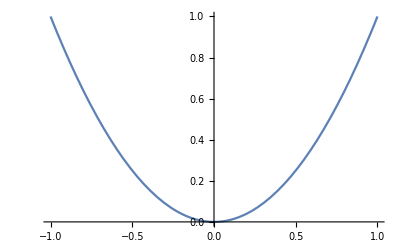

```mathematica
Plot[f[x],{x,-1,1}]
```

From calculus we also now that the concept  of derivative is very useful to measure the rate of “change” a function have at a given point.

```mathematica
f'[x]
```

2 x

```mathematica
f'[1]
```

2

```mathematica
Manipulate[
Block[{f},f[x_]:=x^2;Plot[{f[x],f'[x0](x-x0)+f[x0]},{x,-1,1},PlotRange->{-1/2,3/2},Epilog->{
Inset[TextGrid[{{"Value: ", x0},{"Function: ", f[x0]},{"Derivative: ", f'[x0]}},BaseStyle->12],{.1,.8},Scaled[{0,0}]],
PointSize[.02],Red,Point[{x0,f[x0]}]},
PlotStyle->{Automatic,Red}]],
{{x0,0},-.9,.9}
]
```

## Function and Derivatives

Even complex function like If statements can be differentiated if we pay attention to the boundary conditions.

```mathematica
f[x_]:=Piecewise[{{1/3x^2,x>=0}},-x/2]
```

```mathematica
f'[x]
```

Piecewise[{{-1/2, x<0}, {(2 x)/3, x>0}, {Indeterminate, True}}]

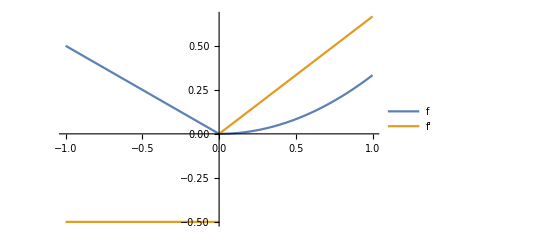

```mathematica
Plot[Evaluate@{f[x],f'[x]},{x,-1,1},PlotLegends->{"f","f'"}]
```

## Function and Predictions

Function can be used to predict values.
The simplest one we can write is a linear model that takes a scalar and returns a scalar
This model depends on two parameters.

```mathematica
f[α_,β_][x_]:=α*x+β
```

```mathematica
Manipulate[
Block[{f},
f[α_,β_][x_]:=α*x+β;
Plot[f[α,β][x],{x,-5,5},PlotRange->3{-1,1},
Epilog->{{GrayLevel[.5,.5],Disk[{0,β},1,{0,Tanh@α}]},
{Black,Thick,Line[{{0,0},{0,β}}],Circle[{0,β},1,{0,Tanh@α}]},
Inset[TextGrid[{{"α ", α},{"β ", β}},BaseStyle->12],{-3,2.8},Scaled[{0,1}]]},AspectRatio->Automatic]
],
{{α,0},-1,1},
{{β,0},-3,3}
]
```

Given a particular choice of the parameter and an input value, the model will predict an output value.

```mathematica
Manipulate[
Block[{f},
f[α_,β_][x_]:=α*x+β;
Plot[f[α,β][x],{x,-5,5},PlotRange->3{-1,1},
Epilog->{
Inset[TextGrid[{{"Value: ", x0},{"Prediction: ", N@f[α,β][x0]}},BaseStyle->12],{1,2.8},Scaled[{0,1}]],
Inset[TextGrid[{{"α ", α},{"β ", β}},BaseStyle->12],{-3,2.8},Scaled[{0,1}]],
{Black,PointSize[.02],Point[{x0,0}],Point[{0,f[α,β][x0]}],PointSize[.01],Point[{x0,f[α,β][x0]}],Dashed,Line[{{x0,0},{x0,f[α,β][x0]},{0,f[α,β][x0]}}]}},AspectRatio->Automatic]
],
{{α,.5},-1,1},
{{β,-1},-3,3},
{{x0,1},-3,3}
]
```

## Function and Classifications

Function can be used to classify values as well.
A non-linear function like the logistic function can turn a prediction into a single class probability.
You can assign the input to one of two classes (binary classification) by thresholding the probability function.

The logistic function in the WL is called LogisticSigmoid

```mathematica
f[α_,β_][x_]:=LogisticSigmoid[α*x+β]
```

```mathematica
classifier[α_,β_][x_]:=If[f[α,β][x]>=.5,"A","B"]
```

```mathematica
Manipulate[
Block[{f},
f[α_,β_][x_]:=LogisticSigmoid[α*x+β];
Plot[{f[α,β][x]},{x,-5,5},PlotRange->{-1/2,2},Epilog->{
Inset[TextGrid[{{"Value: ", x0},{"Prediction: ", N@f[α,β][x0]},{"Classification: ",If[ N@f[α,β][x0]>.5,"A","B"]}},BaseStyle->12],{.3,1.8},Scaled[{0,1}]],
Inset[TextGrid[{{"α ", α},{"β ", β}},BaseStyle->12],{-3,1.8},Scaled[{0,1}]],
{Black,PointSize[.02],Point[{x0,0}],Point[{0,f[α,β][x0]}],PointSize[.01],Point[{x0,f[α,β][x0]}],Dashed,Line[{{x0,0},{x0,f[α,β][x0]},{0,f[α,β][x0]}}]}},
Prolog->{Opacity[.2],If[ N@f[α,β][x0]>.5,Black,Gray],Rectangle[{-5,.5},{5,1}],If[ N@f[α,β][x0]>.5,Gray,Black],Rectangle[{-5,0},{5,.5}]},
PlotStyle->{Automatic},Frame->True,FrameTicks->{Automatic,{0,.5,1}}]],
{{α,1},-3,3},
{{β,0},-3,3},
{{x0,0},-3,3}
]
```

## Predictions and Errors

The data that you have to model will often come in input/output pairs.
Let’s start from some synthetic data that follow a roughly linear behaviour.

```mathematica
data=
```

{{-3.90684,-1.20106},{-3.31021,-1.02281},{-2.26364,-0.909454},{-2.03721,-0.813189},{-1.88821,-0.741908},{-0.976696,-0.544966},{-0.609318,-0.6203},{-0.327863,-0.523252},{-0.165347,-0.511962},{0.175714,-0.306814},{0.350054,-0.26511},{0.670834,-0.284203},{0.703541,-0.294514},{2.07917,-0.0221665},{3.01287,0.119135},{3.07783,0.291442},{3.35648,0.342504},{3.41813,0.310174},{3.87994,0.432349},{3.89832,0.410025}}

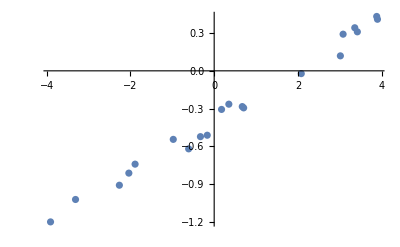

```mathematica
ListPlot[data]
```

When applying the model the input data, the prediction will in principle be incorrect for an arbitrary choice of the model parameters

```mathematica
f[α_,β_][x_]:=α*x+β
```

```mathematica
f[-.3,.1][data[[All,1]]]
data[[All,2]]
```

{1.27205,1.09306,0.779092,0.711162,0.666464,0.393009,0.282795,0.198359,0.149604,0.0472858,-0.00501624,-0.10125,-0.111062,-0.52375,-0.80386,-0.82335,-0.906944,-0.925439,-1.06398,-1.0695}

{-1.20106,-1.02281,-0.909454,-0.813189,-0.741908,-0.544966,-0.6203,-0.523252,-0.511962,-0.306814,-0.26511,-0.284203,-0.294514,-0.0221665,0.119135,0.291442,0.342504,0.310174,0.432349,0.410025}

To asses how good the model is we need to condense these differences in a single number: the error or loss.
It is useful to write it as a function of the  model parameters. A common choice is the average squared difference between the target values and the predicted values.

```mathematica
loss[α_,β_]:=Mean[(f[α,β][data[[All,1]]]-data[[All,2]])^2];
```

Here is a table of the loss while varying the β parameter.

```mathematica
Table[{β,loss[.1,β]},{β,-2,2,.1}]//Short
```

{{-2.,2.77703},{-1.9,2.45772},{-1.8,2.15842},«36»,{1.9,5.14426},{2.,5.60496}}

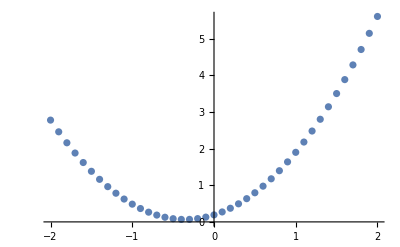

```mathematica
ListPlot[%]
```

## Errors and Training

Minimizing the loss as a function of both α and β leads to their optimal values given the data.
This can be done by taking the derivative respect to the parameters

```mathematica
D[loss[α,β],{{α,β}}]//Simplify
```

{-2.05117+11.7693 α+0.913755 β,0.615608+0.913755 α+2. β}

and finding  the values of α and β that makes it zero.

```mathematica
Solve[D[loss[α,β],{{α,β}}]==0,{α,β}]
```

{{α→0.205468,β→-0.401677}}

```mathematica
Block[{g,min},
min=ArgMin[{loss[α,β],-3<α<3,-3<β<3},{α,β}];
g=Show[Plot3D[loss[α,β],{α,-5,5},{β,-6,6},PlotRangePadding->1,MeshFunctions->{#3&}],Graphics3D[{Black,PointSize[.02],Point[Append[min,loss@@min+5]]}],SphericalRegion->True,Ticks->False]
]
```

-Graphics3D-

A simple, iterative method to find a local minimum is to update the parameters following the (opposite) direction of the gradient. This method is called gradient descent.

```mathematica
Clear[d]
d[α_,β_]=-Normalize[D[loss[α,β],{{α,β}}]];
```

```mathematica
d[3,1]
```

{-0.987934,-0.154878}

```mathematica
Block[{g,min,p={3,1}},
min=ArgMin[{loss[α,β],-3<α<3,-3<β<3},{α,β}];
g=Show[Plot3D[loss[α,β],{α,-5,5},{β,-6,6},PlotRangePadding->1,MeshFunctions->{#3&}],Graphics3D[{Black,PointSize[.02],Point[Append[p,loss@@p+5]],Point[Append[min,loss@@min+5]],
Red,Arrowheads[.004],Thick,Arrow[{Append[p,loss@@p+5],Append[p+d@@p,loss@@(p+d@@p)+5]}]}],SphericalRegion->True,Ticks->False];
Show[g,ViewPoint->N@{-2,4,2}]
]
```

-Graphics3D-

For a well defined error function, nesting the updates with a small update step leads to a fixed point.

```mathematica
ListLinePlot[Transpose@NestList[Function[#+1/500d@@#],{3,1},2000],PlotLabels->{"α","β"}]
```

-Graphics-

When the number of input examples is very large, computing the actual gradient can become very expensive. Sampling the gradient on a subset of the examples (a mini-batch) allows to achieve faster iteration speed and reduce the memory constraints. This method is called stochastic gradient descent.

## Simple Networks

## A Linear Model (again)

The simplest possible learnable program is again a linear model between a scalar input and a scalar output.
This is also the ideal candidate for our fist parametrized, trainable program.

In the WL a trainable affine transformation is called LinearLayer

```mathematica
network=LinearLayer["Input"->1,"Output"->1]
```

LinearLayer[<>]

The parameters α and β are called weights and biases respectively and when the operation is first created  they are unspecified. In order to use the model you have to either train it or initialize it.

You can initialize a network with the function NetInitialize

```mathematica
network=NetInitialize[network,RandomSeeding->1]
```

LinearLayer[<>]

The properties of a LinearLayer (and any other layer) can be accessed using the NetExtract function

Arrays are stored in a typed structure called NumericArray

```mathematica
NetExtract[network,{{"Weights"},{"Biases"}}]
```

{NumericArray[…],NumericArray[…]}

You can use the function Normal to convert them to regular list

```mathematica
{α,β}=Normal[%]
```

{{{0.485679}},{0.}}

Evaluating the model is equivalent to manually perform the affine transformation.

```mathematica
network[{0.5}]
```

{0.242839}

```mathematica
α .{0.5}+β
```

{0.242839}

## A Linear Model (again)

Our affine transformation depends on two learnable parameters which are initialize at random. In almost every case it will not be a good fit for the input data.

```mathematica
data=
```

{-3.90684→-1.20106,-3.31021→-1.02281,-2.26364→-0.909454,-2.03721→-0.813189,-1.88821→-0.741908,-0.976696→-0.544966,-0.609318→-0.6203,-0.327863→-0.523252,-0.165347→-0.511962,0.175714→-0.306814,0.350054→-0.26511,0.670834→-0.284203,0.703541→-0.294514,2.07917→-0.0221665,3.01287→0.119135,3.07783→0.291442,3.35648→0.342504,3.41813→0.310174,3.87994→0.432349,3.89832→0.410025}

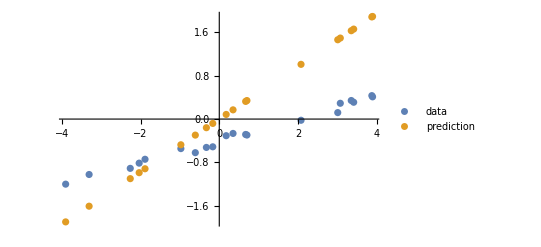

```mathematica
ListPlot[{List@@@data,Transpose@{data[[All,1]],network[data[[All,1]]]}},PlotLegends->{"data","prediction"}]
```

You can have an idea of the error for each data point by plotting the residuals: the difference between the expected value and the predicted value.

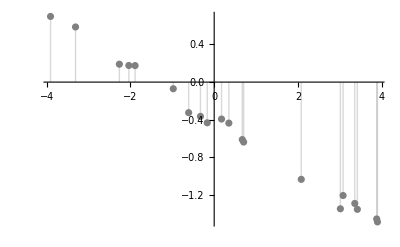

```mathematica
ListPlot[initialerrors=Transpose@{data[[All,1]],data[[All,2]]-network[data[[All,1]]]},Filling->Axis,PlotStyle->Gray]
```

The optimization procedure, typically called training, is attempting a minimization of the sum of the errors, as defined by the error function, or loss.

You can train a network using the NetTrain function, the initial step size can be specified using the LearningRate option

To specify a custom error function for the training, use the LossFunction option
If a loss is not specified one is used automatically depending on the network last layer

The average squared deviation can be computed using MeanSquaredLossLayer

```mathematica
predictor=NetTrain[network,data,LossFunction->MeanSquaredLossLayer[],
LearningRate->10^-4,Method->"SGD",TrainingProgressReporting->{"Panel",}]
```

NetTrain::invindim3: Data provided to port "Input" should be a non-empty list of length-1 vectors, but was a length-20 vector of real numbers.

$Failed

The final values of the parameters make for a much better prediction using the model.

```mathematica
Normal@NetExtract[predictor,{{"Weights"},{"Biases"}}]
```

NetExtract::arg1: First argument $Failed should be a net, NetEncoder, or NetDecoder.

NetExtract[$Failed,{{Weights},{Biases}}]

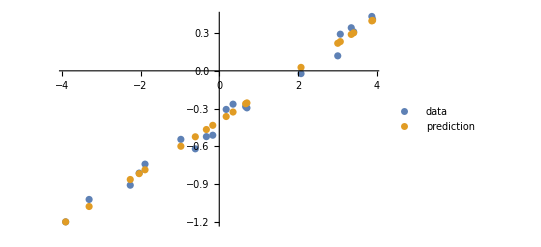

```mathematica
ListPlot[{data,Transpose@{data[[All,1]],predictor[data[[All,1]]]}},PlotLegends->{"data","prediction"}]
```

## Interlude: Layer Properties

### Embedded Gradients

In order to be trainable, network operations must be defined together with their derivative.

You can access the derivative of a layer using NetPortGradient in the second argument

```mathematica
network[.5,NetPortGradient["Input"]]
```

{0.485679}

```mathematica
D[Sin[x^2],x]
```

2 x Cos[x^2]

```mathematica
D[Sin[y],y]D[x^2,x]
```

2 x Cos[y]

```mathematica
D[Sin[y],y]D[x^2,x]/.y->x^2
```

2 x Cos[x^2]

During the training, the optimizer computes the derivative respect to each parameter.

```mathematica
network[.5,NetPortGradient["Weights"]]
```

{{0.5}}

```mathematica
network[.5,NetPortGradient["Biases"]]
```

{1.}

The derivative values are accumulated when the model is evaluated on multiple inputs (the mini-batch).

```mathematica
network[{{.5},{-.3},{.1}},NetPortGradient["Weights"]]
```

{{0.3}}

## Interlude: Layer Properties

### Evaluation Device

All the layer operations are defined both on CPU and GPU.
GPU evaluation is typically much faster on large networks.

The device used for evaluation and training can  be selected using the TargetDevice option

```mathematica
network[.5,TargetDevice->"CPU"]
```

{0.242839}

```mathematica
network[.5,TargetDevice->"GPU"]
```

{0.242839}

NB: GPU evaluation is not supported on every platform

```mathematica
network[.5,TargetDevice->"GPU"]
```

LinearLayer::trgdevmac: TargetDevice -> "GPU" is not supported on Mac OS platforms.

$Failed

## Interlude: Layer Properties

### General Information

The function Information gives a summary of a layer properties

```mathematica
Information[network]
```

Net Information

It can also be used to access individual properties

```mathematica
Information[network,"Properties"]
```

{Arrays,ArraysByteCounts,ArraysCount,ArraysDimensions,ArraysElementCounts,ArraysLearningRateMultipliers,ArraysList,ArraysPositionList,ArraysSizes,ArraysTotalByteCount,ArraysTotalElementCount,ArraysTotalSize,FullSummaryGraphic,InputForm,InputPortNames,InputPorts,Layers,LayersCount,LayersGraph,LayersList,LayerTypeCounts,MXNetNodeGraph,MXNetNodeGraphPlot,OutputPortNames,OutputPorts,Properties,RecurrentStatesCount,RecurrentStatesPositionList,SharedArraysCount,SummaryGraphic,TopologyHash}

```mathematica
Information[network,"ArraysDimensions"]
```

<|{Biases}→{1},{Weights}→{1,1}|>

NetExtract[…, All] can also be use to extract all the layers parameters

```mathematica
NetExtract[network,All]
```

<|Biases→NumericArray[…],OutputDimensions→{1},Weights→NumericArray[…]|>

## Classification: two-classes

A very common machine learning task is data classification. Here we have two clusters of point and the task is to learn to assign the data coming from each cluster to a different class.

```mathematica
SeedRandom[1234];
data={
{2,2}+#&/@RandomVariate[NormalDistribution[0,1],{10,2}],
{-3,-3}+#&/@RandomVariate[NormalDistribution[0,1],{10,2}]
}
```

{{{1.49166,1.9294},{0.406104,3.53659},{4.67802,0.683169},{0.905435,2.14295},{2.10417,0.326891},{2.03575,2.17019},{2.93468,1.17314},{1.90904,3.03341},{1.63647,2.18859},{1.86386,1.91605}},{{-2.44197,-5.16128},{-2.99002,-3.85103},{-3.90764,-4.00052},{-2.51024,-2.61744},{-3.45156,-1.85948},{-2.85283,-2.31396},{-1.71998,-4.21146},{-3.58007,-4.20655},{-2.4431,-2.97262},{-3.41428,-2.17271}}}

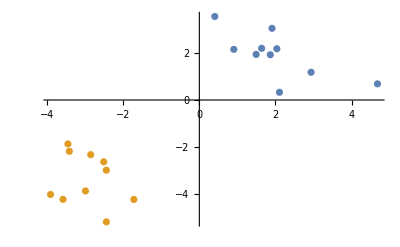

```mathematica
ListPlot[data]
```

In this case the classifier will take a two-dimensional input.

```mathematica
Show[
ListPointPlot3D[{
Append[#,0]&/@data[[1]],
Append[#,1]&/@data[[2]]
},PlotStyle->Black],
Plot3D[LogisticSigmoid[-x-y],{x,-5,5},{y,-5,5},PlotStyle->GrayLevel[.5,.5]]
]
```

-Graphics3D-

This is again modeled with a linear transformation that is converted into a probability using the logistic function.

Multiple layers can be combined using the NetChain function

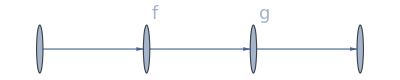
-Graphics-
x↦g(f(x))

```mathematica
Column[{Graph[{1->2,2->3,3->4},VertexLabels->{2-> Style["f",18],3-> Style["g",18]}],TraditionalForm[Style[x|->g[f[x]],16,"Math"]]},Alignment->Center,Spacings->2]
```

Elementwise operation on arrays can be specified using ElementwiseLayer

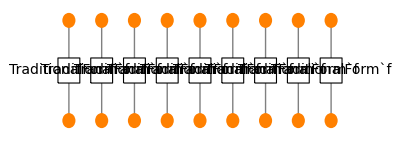

```mathematica
Block[
{h=4,r=0.3,layer0Pts,layer1Pts},
layer0Pts=Thread[{1.5 Range[0,8],h}];
layer1Pts=Thread[{1.5 Range[0,8],0}];
Graphics[
{{Gray,MapThread[Line[{##}]&,{layer1Pts,layer0Pts}]},
{FaceForm[White],EdgeForm[{Thin,Black}],Map[{Rectangle[#-1/2,#+1/2],Text[Style["TraditionalForm`f",14],#]}&,Thread[{1.5 Range[0,8],h/2}]]},
{FaceForm[Orange],Map[Disk[#,r]&,layer0Pts],Map[Disk[#,r]&,layer1Pts]}
}
]
]
```

```mathematica
classifier=NetChain[
{
LinearLayer["Input"->2,"Output"->"Real"],
ElementwiseLayer[LogisticSigmoid]
}
]
```

NetChain[<>]

As training data we use the probability of being part of first class, which is 1 for the points of the first cluster and 0 for the points of the  second cluster.

```mathematica
training=Catenate[Thread/@Thread[data->{1,0}]]
```

{{1.49166,1.9294}→1,{0.406104,3.53659}→1,{4.67802,0.683169}→1,{0.905435,2.14295}→1,{2.10417,0.326891}→1,{2.03575,2.17019}→1,{2.93468,1.17314}→1,{1.90904,3.03341}→1,{1.63647,2.18859}→1,{1.86386,1.91605}→1,{-2.44197,-5.16128}→0,{-2.99002,-3.85103}→0,{-3.90764,-4.00052}→0,{-2.51024,-2.61744}→0,{-3.45156,-1.85948}→0,{-2.85283,-2.31396}→0,{-1.71998,-4.21146}→0,{-3.58007,-4.20655}→0,{-2.4431,-2.97262}→0,{-3.41428,-2.17271}→0}

During the training, the classifier line is (should be) updated to divide the two clusters according to their class.

```mathematica
classifier2=NetTrain[classifier,training,TrainingProgressReporting->{"ProgressIndicator",}]
```

NetChain[<>]

The classifier is now trained and its result are matching the training examples.

```mathematica
classifier2[training[[All,1]]]
Round[%]
training[[All,2]]
```

{0.642515,0.683601,0.673522,0.635957,0.585773,0.667844,0.648224,0.700973,0.65797,0.652088,0.219297,0.253624,0.228218,0.314115,0.321797,0.318069,0.269375,0.228034,0.301049,0.309542}

{1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0}

{1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0}

## Classification: three-classes

In the previous example we have used the fact the the probabilities of belonging to all classes must sum to 1 in order to represent them using a single scalar value. With three or more classes this is not possible any more.

```mathematica
SeedRandom[1234];
data={
{2,2}+#&/@RandomVariate[NormalDistribution[0,1],{10,2}],
{-1,2}+#&/@RandomVariate[NormalDistribution[0,1],{10,2}],
{-3,-3}+#&/@RandomVariate[NormalDistribution[0,1],{10,2}]
};
```

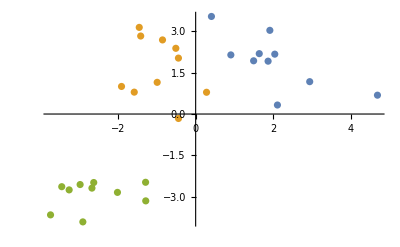

```mathematica
ListPlot[data]
```

The new classifier will output a probability value for each class. Do do it we update the linear layer to have three outputs. To make that a probability vector, a typical choice is the softmax function.

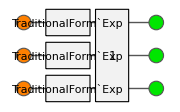

You can perform a softmax normalization using SoftmaxLayer

```mathematica
classifier=NetInitialize@NetChain[
{
LinearLayer["Input"->2,"Output"->3],
SoftmaxLayer[]
}
]
```

NetChain[<>]

```mathematica
classifier[{.3,.1}]
```

{0.271007,0.241171,0.487822}

In many frameworks, input pre-processing and output post-processing can be used to handle comparison with non vector quantities. In this case is convenient to convert the probability vector the the best class using an arg-max operation.

The input and  output of a network can be processed using the functions NetEncoder and NetDecoder

Use the “Class” decoder to apply the arg-max operation to a vector and return the correspondent class

A previously defined network can be modified using the function NetReplacePart

```mathematica
classifier2=NetReplacePart[
classifier,
"Output"->NetDecoder[{"Class",{"A","B","C"}}]
]
```

NetChain[<>]

```mathematica
classifier2[{.3,.1}]
```

C

```mathematica
classifier2[{.3,.1},"Probabilities"]
```

<|A→0.271007,B→0.241171,C→0.487822|>

The training data is the list of points with their correspondent class.

```mathematica
training=Catenate[Thread/@Thread[data->{"A","B","C"}]]
```

{{1.49166,1.9294}→A,{0.406104,3.53659}→A,{4.67802,0.683169}→A,{0.905435,2.14295}→A,{2.10417,0.326891}→A,{2.03575,2.17019}→A,{2.93468,1.17314}→A,{1.90904,3.03341}→A,{1.63647,2.18859}→A,{1.86386,1.91605}→A,{-0.441969,-0.161282}→B,{-0.99002,1.14897}→B,{-1.90764,0.999477}→B,{-0.510242,2.38256}→B,{-1.45156,3.14052}→B,{-0.852832,2.68604}→B,{0.280016,0.788536}→B,{-1.58007,0.79345}→B,{-0.443105,2.02738}→B,{-1.41428,2.82729}→B,{-2.90257,-3.90993}→C,{-2.01197,-2.84016}→C,{-3.734,-3.65546}→C,{-3.44536,-2.63376}→C,{-3.25531,-2.74969}→C,{-2.66868,-2.68532}→C,{-1.28423,-3.14765}→C,{-2.62253,-2.48283}→C,{-2.97288,-2.55598}→C,{-1.28834,-2.47378}→C}

The target of this training is a probability distribution, so the Euclidean distance between the probability vectors is not a good measure of the error. The loss function used for classification training is typically the cross entropy, which measure the difference between a probability distribution and a second, reference probability distribution.

When using a network ending with a SoftmaxLayer, a CrossEntropyLossLayer is automatically used as loss function

```mathematica
classifier3=NetTrain[classifier2,training,TrainingProgressReporting->{"ProgressIndicator",}]
```

NetChain[<>]

```mathematica
classifier3[training[[All,1]]]
training[[All,2]]
```

{A,A,A,A,A,A,A,A,A,A,B,B,B,B,B,B,B,B,B,B,C,C,C,C,C,C,C,C,C,C}

{A,A,A,A,A,A,A,A,A,A,B,B,B,B,B,B,B,B,B,B,C,C,C,C,C,C,C,C,C,C}

## Data encoding

In some cases we might have some prior knowledge about the type of function we are trying to model.
Here the target function is a linear combination of some non-liner transformation of the input.

```mathematica
Clear[f]
f[{x_,y_}]:=1-2x+.3x^2+3y+RandomReal[{-2,2}]
```

In this case we can move the non-linear part to the data pre-processing and still use our previous predictor.

```mathematica
encoderFunction[{x_,y_}]:={1,x,x^2,y,y^2}
```

```mathematica
encoderFunction[{.4,-.2}]
```

{1,0.4,0.16,-0.2,0.04}

The “Function” encoder can perform an arbitrary transformation

```mathematica
encoder=NetEncoder[{"Function",encoderFunction,{5}}]
```

NetEncoder[<>]

```mathematica
encoder[{.4,-.2}]
```

{1.,0.4,0.16,-0.2,0.04}

The encoder can then be assigned to a network port  or even a layer port

```mathematica
network=NetChain[
{
LinearLayer["Output"->"Real"]
},
"Input"->encoder
]
```

NetChain[<>]

```mathematica
LinearLayer["Output"->"Real","Input"->encoder]
```

LinearLayer[<>]

Other useful encoders include “Image”, “Audio”, “Tokens”, “Video” and more

```mathematica
imageencoder=NetEncoder[{"Image",{5,5}}]
```

NetEncoder[<>]

```mathematica
imageencoder[-Graphics-]//Map[MatrixForm]
```

{(1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1.
1. | 1. | 0. | 0. | 0.
0.5 | 0.5 | 0.5 | 0. | 0.
0.5 | 0.5 | 0.5 | 0. | 0.),(0. | 0. | 0.5 | 0.5 | 0.5
0. | 0. | 0.5 | 0.5 | 0.5
0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.),(0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 1.
0.5 | 0.5 | 0.5 | 1. | 1.
0.5 | 0.5 | 0.5 | 1. | 1.)}

## Training and Validation

For this training, we generate some more data from a slightly larger domain to check how well the model is generalizing.
This data is generally called validation data and is important to keep it separate from the training data.

```mathematica
SeedRandom[1234];
training={#,f[#]}&/@RandomReal[{-10,10},{100,2}];
validation={#,f[#]}&/@RandomReal[{-20,20},{50,2}];
```

```mathematica
ListPointPlot3D[{Append@@@training,Append@@@validation},PlotStyle->{Red,Blue},PlotLegends->{"training","validation"}]
```

-Graphics3D-

In this case, training the linear combination of non linear functions generalizes well to the validation set.

```mathematica
linearfit=NetTrain[network,Rule@@@training,ValidationSet->Rule@@@validation]
```

NetChain[<>]

```mathematica
Show[
ListPointPlot3D[{Append@@@training,Append@@@validation},PlotStyle->{Red,Blue},PlotLegends->{"training","validation"}],
Plot3D[linearfit[{x,y}],{x,-20,20},{y,-20,20},Lighting->{{"Ambient", White}}]
]
```

-Graphics3D-

## Deeper Networks

## Nonlinear regression

It is not always possible to solve a regression problem with a linear model or to know in advance a non-linear encoding of the data that turns the problem into a linear one.
The real power of neural networks is to build a function approximator stacking a sequence of linear transformation followed by a non-linear function.

The non-linear part, often called transfer function, activation function or simply non-linearity, is an essential element, without it a sequence of linear model is just a more elaborate way to specify a single linear model.

Linear and elementwise operation are so popular that they can be specified in a compact form

The network internally works on tensor data, you can use an extra layer like SummationLayer to collapse it into a scalar

```mathematica
network=NetChain[{10,Tanh,10,Tanh,1,SummationLayer[]}]
```

NetChain[<>]

In this case we use a linear transformation that recombines the 2-dimensional input in a higher dimensional space (10), making hopefully easy for the model the task of finding the proper coefficients. This type of non-trainable settings are called hyper-parameters and in general are not easy to optimize.

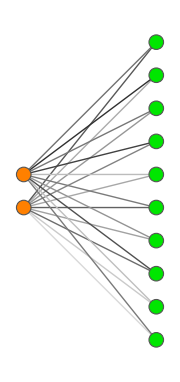
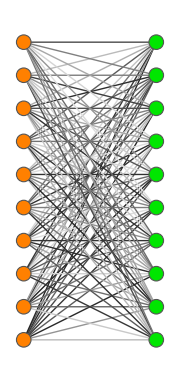
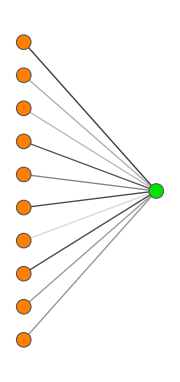
```mathematica
Row[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},Spacer[20]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

Each linear layer is a generalization of a simple linear transformation.

```mathematica
Block[{in=5,out=10},TableForm[{{MatrixForm @ Table[Row[{Spacer[out],Style[●,RGBColor[1, 0.5, 0]],Spacer[out]}], {j, 1}, {k, in}],Spacer[1],Spacer[1],Spacer[1],Spacer[1]}, {
  MatrixForm @ Table[Indexed[HoldForm[α], {j, k}], {j, out}, {k, in}],"+",
MatrixForm @ Table[Indexed[HoldForm[β], {j}], {j, out}, {k, 1}]," = ",
MatrixForm @ Table[Style[●,RGBColor[0, 0.9, 0]], {j, out}, {k, 1}]
}}]]
```

(● | ● | ● | ● | ●) |  |  |  | 
(α11 | α12 | α13 | α14 | α15
α21 | α22 | α23 | α24 | α25
α31 | α32 | α33 | α34 | α35
α41 | α42 | α43 | α44 | α45
α51 | α52 | α53 | α54 | α55
α61 | α62 | α63 | α64 | α65
α71 | α72 | α73 | α74 | α75
α81 | α82 | α83 | α84 | α85
α91 | α92 | α93 | α94 | α95
α101 | α102 | α103 | α104 | α105) | + | (β1
β2
β3
β4
β5
β6
β7
β8
β9
β10) |  =  | (●
●
●
●
●
●
●
●
●
●)

You can use NetTrain[network, data, All, …] to get a NetTrainResultsObject that contains much information about the training (including the trained model)

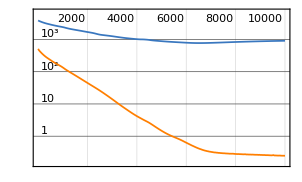
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:20000  rounds:10000  time:37s  examples/s:35403
data | ,,  training examples:100  validation examples:50  processed examples:1280000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.51×10^-1
validation | ,,  loss:9.09×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
nonlinearfitTraining=NetTrain[network,Rule@@@training,All,ValidationSet->Rule@@@validation]
```

```mathematica
nonlinearfitTraining["ValidationLoss"]
```

908.84

The effect of the specific activation function used is very visible in the extrapolation region.

```mathematica
nonlinearfit=nonlinearfitTraining["TrainedNet"]
```

NetChain[<>]

```mathematica
Show[
Plot3D[nonlinearfit[{x,y}],{x,-30,30},{y,-30,30},Lighting->{{"Ambient", White}},PlotRange->1.5MinMax@validation[[All,2]]],
ListPointPlot3D[{Append@@@training,Append@@@validation},PlotStyle->{Red,Blue},PlotLegends->{"training","validation"}],
PlotRangePadding->10
]
```

-Graphics3D-

## Activation Functions

The choice of a good activation function is very important: it affect evaluation speed, extrapolation bias and most importantly the gradient computation for the whole network.

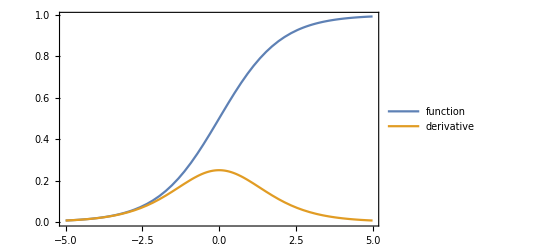
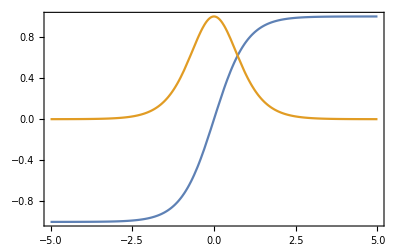
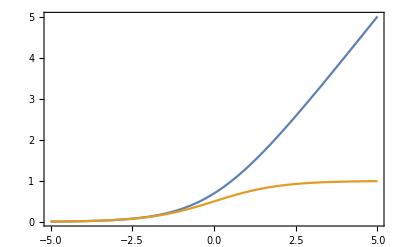
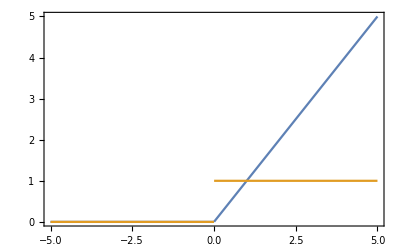
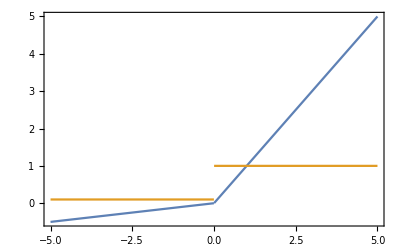
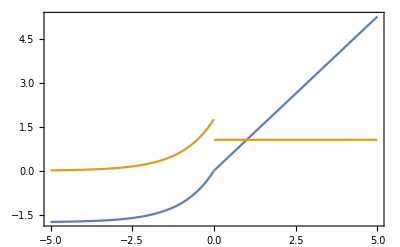
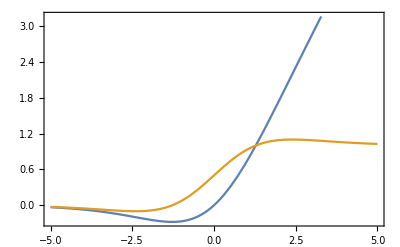
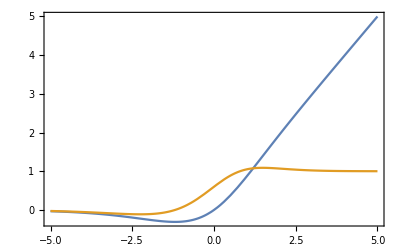
Logistic Sigmoid | Tanh | SoftPlus
-Graphics- | -Graphics- | -Graphics-
ReLU | LeakyReLU | SELU
-Graphics- | -Graphics- | -Graphics-
Swish | Mish | 
-Graphics- | -Graphics- |

```mathematica
Legended[Grid[Catenate[Transpose/@Partition[MapThread[
{#1,Plot[Evaluate@{#2[x],D[#2[x],x]},{x,-5,5},Frame->True]}&,{{"Logistic Sigmoid","Tanh","SoftPlus","ReLU","LeakyReLU","SELU","Swish","Mish"},{LogisticSigmoid,Tanh,Log[1+Exp[#]]&,Ramp,Ramp[#]-.1Ramp[-#]&,1.7581 (Exp[-Ramp[-#]]-1)+Ramp[#]*1.0507&,#*LogisticSigmoid[#]&,# Tanh[Log[1+Exp[#]]]&}}
],3,3,1,{}]],Alignment->Center,BaseStyle->"Text"],Placed[LineLegend[ColorData[97]/@{1,2},{"function","derivative"},LegendLayout->"Row"],Above]]
```

Let’s try a different activation for the last problem.

You can replace layers based on a pattern using NetReplace

```mathematica
network2=NetReplace[
network,
ElementwiseLayer[Tanh]->ElementwiseLayer["Swish"]
]
```

NetChain[<>]

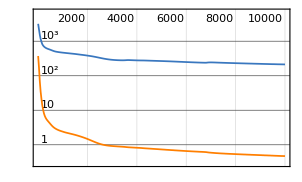
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:20000  rounds:10000  time:33s  examples/s:39368
data | ,,  training examples:100  validation examples:50  processed examples:1280000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:4.7×10^-1
validation | ,,  loss:2.13×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
nonlinearfitTraining2=NetTrain[network2,Rule@@@training,All,ValidationSet->Rule@@@validation]
```

The new activation gives a smaller validation loss.

```mathematica
nonlinearfitTraining2["ValidationLoss"]
```

212.522

```mathematica
nonlinearfit2=nonlinearfitTraining2["TrainedNet"]
```

NetChain[<>]

```mathematica
Show[
Plot3D[nonlinearfit2[{x,y}],{x,-30,30},{y,-30,30},Lighting->{{"Ambient", White}},PlotRange->1.5MinMax@validation[[All,2]]],
ListPointPlot3D[{Append@@@training,Append@@@validation},PlotStyle->{Red,Blue},PlotLegends->{"training","validation"}],
PlotRangePadding->10
]
```

-Graphics3D-

## Computational graphs

So far we have only seen networks implementing a sequence of operations with a single input and output.
Neural networks are more general than that and they can represent also operation with multiple inputs and output.

To demonstrate that, let’s implement the computational graph of MeanSquaredLossLayer.

Use the NetGraph construct to construct a directed acyclic graph

```mathematica
h(g(x),f(x))↦y
```

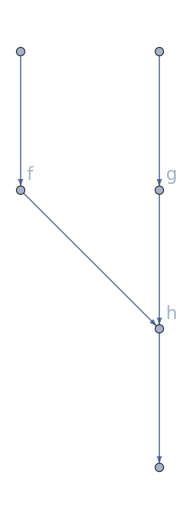

```mathematica
Graph[{1->2,3->4,2->5,4->5,5->6},VertexLabels->{2-> Style["f",18],4-> Style["g",18],5-> Style["h",18]},ImageSize->Small]
```

Network input and output can be explicitly created and used with the NetPort symbol

You can perform elementwise operation with multiple inputs using ThreadingLayer

Use AggregationLayer to combine data along one or more array axes

```mathematica
meansquaredloss=NetGraph[
{ThreadingLayer[Subtract],ElementwiseLayer[#^2&],AggregationLayer[Mean,All]},
{NetPort["Input"]->1,NetPort["Target"]->1,1->2,2->3}
]
```

NetGraph[<>]

The result is the same as the built-in layer.

```mathematica
meansquaredloss[<|"Input"->{.1,-.3,1.5},"Target"->{.5,-.2,1.2}|>]
```

0.0866667

```mathematica
MeanSquaredLossLayer[][<|"Input"->{.1,-.3,1.5},"Target"->{.5,-.2,1.2}|>]
```

0.0866667

## Computational graphs

Another example of network graph is a classifier that handles different types of inputs.

The Titanic survival dataset contains String and Quantity expressions

```mathematica
titanicdata=DeleteMissing[ResourceData["Sample Data: Titanic Survival"],1,2];
```

```mathematica
First[titanicdata]
```

Use the appropriate encoders and decoders on each port

Multiple arrays can be joined together using CatenateLayer

```mathematica
titanicnet=NetGraph[
{"SexFeatures"->5,
"ClassFeatures"->5,
"AgeFeatures"->5,
"Features"->CatenateLayer[],
"Classifier"->{15,ElementwiseLayer["Swish"],15,ElementwiseLayer["Swish"],2,SoftmaxLayer[]}
},
{NetPort["Sex"]->"SexFeatures",
NetPort["Class"]->"ClassFeatures",
NetPort["Age"]->"AgeFeatures",
{"SexFeatures","ClassFeatures","AgeFeatures"}->"Features"->"Classifier"->NetPort["SurvivalStatus"]
},
"Sex"->NetEncoder[{"Class",{"male","female"},"IndicatorVector"}],
"Class"->NetEncoder[{"Class",{"1st","2nd","3rd"},"IndicatorVector"}],
"Age"->NetEncoder[{"Function",QuantityMagnitude,"Real"}],
"SurvivalStatus"->NetDecoder[{"Class",{"survived","died"}}]
]
```

NetGraph[<>]

Remember to keep some data aside for validation!

```mathematica
SeedRandom[1234];
{training,validation}=TakeDrop[RandomSample[titanicdata],800];
```

A common technique to manage the training time is to keep an eye on the validation error.

Use the TrainingStoppingCriterion option to control early stopping during the training

Use the TrainingProgressMeasurements option to perform additional measurements

```mathematica
titanicnet2=NetTrain[
titanicnet,training,All,ValidationSet->validation,
TrainingStoppingCriterion-><|"Criterion"->"Loss","InitialPatience"->100,"Patience"->10|>,
TrainingProgressMeasurements->{"Accuracy","Precision","Recall","ErrorRate"}
]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1456  rounds:112  time:4.0s  examples/s:23300
data | ,,  training examples:800  validation examples:246  processed examples:93184  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:4.09×10^-1  acc.:81.5%  prec.:82.6%  recall:78.9%  error:18.5%
validation | ,,  loss:4.97×10^-1  acc.:79.7%  prec.:79.3%  recall:78.5%  error:20.3%
 | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
RandomChoice[validation,4]//Transpose
titanicnet2["TrainedNet"][Normal[%]]
```

{survived,died,survived,died}

## References

NeuralNetworks main guide page

NeuralNetworks tutorial

Machine Learning courses on Wolfram U

## Exploration: Losses

Background

The loss layers specifies the functional form of loss to be computed, which measures the compatibility between a prediction (e.g. the class scores in classification) and the actual value of the label. The data loss takes the form of an average over the data losses for every individual example. In the iteration of training the network, this explicit loss function is minimized by tuning the parameters (via back propagation). When a loss layer is chosen automatically for a port, the loss layer to use is based on the layer within the net whose output is connected to the port. For SoftmaxLayer and LogisticSigmoid, CrossEntropyLossLayer is chosen, for non-loss layers, MeanSquaredLossLayer is chosen. If a loss layer is specified, it is used unchanged. You can also specify custom losses using the option LossFunction.

### Examples of some implemented loss layers

MeanSquaredLossLayer : represents a loss layer that computes the mean squared difference between the "Input" port and "Target" port. (Gaussian type used for regression problem)

```mathematica
data=<|"Input"-> {1,2,3},"Target"->{3,2,1}|>;
MeanSquaredLossLayer[][data]
meanSquaredLoss=N[Mean[Flatten[(#Input-#Target)^2]]]&; 
meanSquaredLoss[data]//N
```

2.66667

2.66667

CrossEntropyLossLayer : represents a net layer that computes the information- theoretic distance by comparing probabilities with specified target values. (used for classification problem)

```mathematica
data=<|"Input"-> {0.1,0.2,0.7},"Target"->{0.12,0.3,0.6}|>;
CrossEntropyLossLayer["Probabilities"][data]
ceLoss=-Total[#Target*Log@#Input]&;
ceLoss[data]
```

0.973147

0.973147

Implement a MeanSquareAbsoluteLoss using ThreadingLayer.

Hint: Refer to the documentation of "ThreadingLayer"paclet:ref/ThreadingLayer

```mathematica
meansquareloss=NetGraph[{ThreadingLayer[(#1-#2)^2&]},{{NetPort["Input"],NetPort["Target"]}->1},"Input"->"Real"]
```

NetGraph[<>]

Perform linear regression using the created layer on the following layer: data={1→1, 2→2, 3→3, 4→9, 5→5}.

```mathematica
data={1->1,2->2,3->3,4->9,5->5};
trained=NetTrain[LinearLayer[],data,LossFunction->meansquareloss,MaxTrainingRounds->10000]
```

LinearLayer[<>]

Plot the solution.

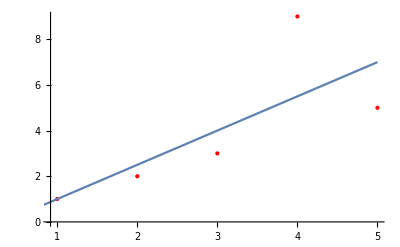

```mathematica
dataPlot=ListPlot[List@@@data,PlotStyle->{Red,PointSize[Medium]}];
Show[dataPlot,Plot[trained[x],{x,0,5}]]
```

Do a validation of your implementation by comparing the solution with the implemented MeanSquaredLossLayer[].

```mathematica
{net1,net2}=NetTrain[LinearLayer[],data,LossFunction->#1,MaxTrainingRounds->10000]&/@{MeanSquaredLossLayer[],meansquareloss};
```

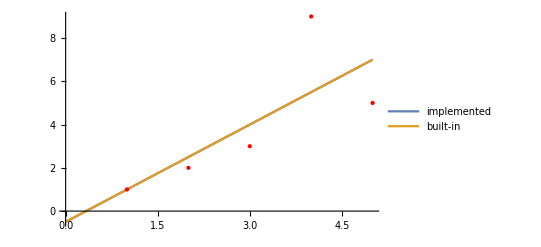

```mathematica
Show[
Plot[{Legended[net1[x],"implemented"],Legended[net2[x],"built-in"]},{x,0,5},PlotRange->All],
dataPlot]
```

You can further repeat the same experiment with the functional form of MeanAbsoluteLossLayer[]

## Exploration: Debugging

Identify the mistake in the code:

```mathematica
lenet2=NetChain[{500,Ramp,12,SoftmaxLayer[]},
"Input"->1000, "Output"->NetDecoder[{"Class",Range[0,9]}]  
]
```

NetChain::tyfail2: Inferred inconsistent dimensions for output of layer 4 (a length-10 vector of real numbers versus a length-12 vector of real numbers).

$Failed

## Exploration: Regularization andNetwork Training

Generate a noisy data, by adding random noise , with an underlying gaussian distribution and visualize it.

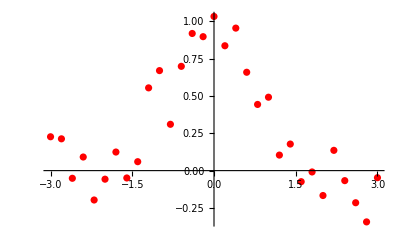

```mathematica
data=Table[x->Exp[-x^2]+RandomVariate[NormalDistribution[0,.15]],{x,-3,3,.2}];
plot=ListPlot[List@@@data,PlotStyle->Red]
```

Use a low “capacity” perceptron network for training.

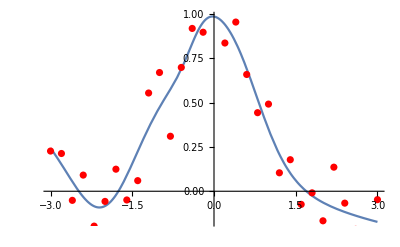

```mathematica
net=NetChain[{5,Tanh,1},"Input"->"Scalar","Output"->"Scalar"];
net3=NetTrain[net,data,Method->"ADAM"];
Show[Plot[net3[x],{x,-3,3}],plot]
```

Train the network with a “large” capacity perceptron model.

```mathematica
net=NetChain[{150,Tanh,150,Tanh,1},"Input"->"Scalar","Output"->"Scalar"];
net1=NetTrain[net,data,Method->"ADAM"];
```

Visualize the training to see how the model overfits to the noise.

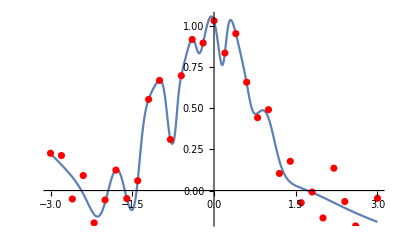

```mathematica
Show[Plot[net1[x],{x,-3,3}],plot]
```

Now add a “Regularization” parameter  to NetTrain to prevent overfitting (hint: look at the documentation page for NetTrain under the Method option).

Hint:  look at the documentation page for NetTrain under the Method option

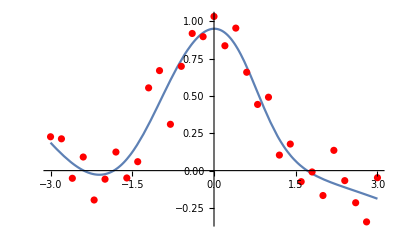

```mathematica
net2=NetTrain[net,data,Method->{"ADAM","L2Regularization"->0.001}];
Show[Plot[net2[x],{x,-3,3}],plot,PlotRange->All]
```

Stop the training immediately and visualize the results.

```mathematica
net=NetChain[{150,Tanh,150,Tanh,1},"Input"->"Scalar","Output"->"Scalar"];
net3=NetTrain[net,data,Method->"ADAM"];
Show[Plot[net3[x],{x,-3,3}],plot]
```

-Graphics-

Do it programmatically using the TrainingStoppingCriterionpaclet:ref/TrainingStoppingCriterion

```mathematica
net4=NetTrain[net,data,Method->"ADAM",TrainingStoppingCriterion-><|"Criterion"->"Loss", "AbsoluteChange"->0.00001|>];
Show[Plot[net3[x],{x,-3,3}],plot]
```

NetTrain::novalidation: No validation set provided, defaulting to training set for stopping criterion.

-Graphics-

An alternate approach is to use DropoutLayer. It represents a net layer that sets its input elements to zero with probability 0.5 during training and is a commonly used form of regularization.

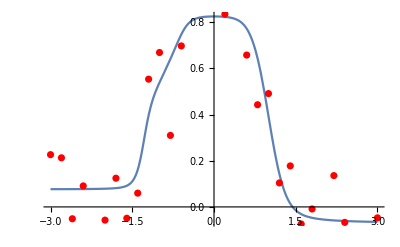

```mathematica
net=NetChain[{150,Tanh,DropoutLayer[0.8],150,Tanh,DropoutLayer[0.8],1},"Input"->"Scalar","Output"->"Scalar"];
net3=NetTrain[net,data,Method->"ADAM"];
Show[Plot[net3[x],{x,-3,3}],plot]
```